# ChernoffFace

Make Chernoff face diagrams

## DefinitionDefinitionDefine your function using the name you gave in the Title line above. You can add input cells and extra code to define additional input cases or prerequisites. All definitions, including dependencies, will be included in the generated resource function. This section should be evaluated before creating the Examples section below.

```mathematica
(************************************************************)
(*Variables rescale*)
(************************************************************)
Clear[VariablesRescale];

Options[VariablesRescale]={"StandardizingFunction"->(Standardize[#,Mean,StandardDeviation]&),"RescaleRangeFunction"->MinMax};

VariablesRescale[data_,opts:OptionsPattern[]]:=Block[{stFunc,rangeFunc},stFunc=OptionValue[VariablesRescale,"StandardizingFunction"];
rangeFunc=OptionValue[VariablesRescale,"RescaleRangeFunction"];
Transpose@Map[Clip[Rescale[#,rangeFunc[#],{0,1}],{0,1}]&,stFunc/@Transpose[data]]]/;MatrixQ[data,NumberQ];


Clear[PrototypeDeviationsRescale];

PrototypeDeviationsRescale[prototypeItem_,items_]:=Block[{},(*If QuartileDeviation the {0,3} range is the same as the upper bound obtained from OutlierIdentifiers::SPLUSQuartileIdentifierParameters.*)Transpose@Map[Clip[Rescale[Standardize[#,0&,StandardDeviation],{0,3},{0.5,1}],{0,1}]&,Transpose@Map[#-prototypeItem&,items]]];


(************************************************************)
(*ChernoffFace Parameters*)
(************************************************************)

DefaultChernoffFaceParameters[]:=<|"FaceLength"->0.5,"ForeheadShape"->0.5,"EyesVerticalPosition"->0.5,"EyeSize"->0.5,"EyeSlant"->0.5,"LeftEyebrowSlant"->0.5,"LeftIris"->0.5,"NoseLength"->0.5,"MouthSmile"->0.5,"LeftEyebrowTrim"->0.5,"LeftEyebrowRaising"->0.5,"MouthTwist"->0.5,"MouthWidth"->0.5,"RightEyebrowTrim"->0.5,"RightEyebrowRaising"->0.5,"RightEyebrowSlant"->0.5,"RightIris"->0.5,"FaceColor"->Automatic,"IrisColor"->Automatic,"NoseColor"->Automatic,"MouthColor"->Automatic,"EyeBallColor"->Automatic,"MakeSymmetric"->True|>;

Clear[ChernoffFacePartsParameters];
ChernoffFacePartsParameters[]:=Pick[ChernoffFace["Properties"],Not/@StringMatchQ[Keys[ChernoffFace["Properties"]],___~~("Color"|"Symmetric")]];


(************************************************************)
(*MakeSymmetricChernoffFaceParameters*)
(************************************************************)

Clear[MakeSymmetricChernoffFaceParameters];

MakeSymmetricChernoffFaceParameters[pars_Association,defaultPars:(_Association|{}):{}]:=Block[{symPairs,res},symPairs={{"LeftEyebrowTrim","RightEyebrowTrim",#&},{"LeftEyebrowRaising","RightEyebrowRaising",#&},{"LeftEyebrowSlant","RightEyebrowSlant",#&},{"LeftIris","RightIris",1-#&}};
res=Association@@Fold[Which[KeyExistsQ[pars,#2[[1]]]&&!KeyExistsQ[pars,#2[[2]]],Append[#1,#2[[2]]->#2[[3]][pars[#2[[1]]]]],!KeyExistsQ[pars,#2[[1]]]&&KeyExistsQ[pars,#2[[2]]],Append[#1,#2[[1]]->#2[[3]][pars[#2[[2]]]]],True,#1]&,{},symPairs];
If[defaultPars==={},Merge[{pars,res},First],Merge[{pars,res,defaultPars},First]]];


(************************************************************)
(*ChernoffFace*)
(************************************************************)

Clear[ChernoffFace];

SyntaxInformation[ChernoffFace]={"ArgumentsPattern"->{_.,OptionsPattern[]}};

Options[ChernoffFace]=Join[{ColorFunction->None,"MakeSymmetric"->Automatic},Options[VariablesRescale],Options[Graphics]];

ChernoffFace::pars="The first argument is expected to be an association, a numeric list, a list of associations, or a list of numeric lists.";
ChernoffFace::colfunc="The value of the option ColorFunction is expected to have the form ColorDataFunction[___] or be one of None or Automatic.";
ChernoffFace::sarg="Chernoff faces summaries are made for lists of numerical vectors or lists of associations.";

ChernoffFace["Properties"]:=DefaultChernoffFaceParameters[];
ChernoffFace["FaceParts"]:=ChernoffFacePartsParameters[];
ChernoffFace["FacePartsProperties"]:=ChernoffFacePartsParameters[];

ChernoffFace[opts:OptionsPattern[]]:=Block[{asc},asc=AssociationThread[Keys[ChernoffFace["FacePartsProperties"]]->RandomReal[1,Length[ChernoffFace["FacePartsProperties"]]]];
asc=Pick[asc,StringMatchQ[Keys[asc],StartOfString~~Except["R"]~~__]];
ChernoffFace[asc,opts]];

ChernoffFace[vec_?(VectorQ[#,NumberQ]&),opts:OptionsPattern[]]:=Block[{mn,mx,pars},pars=Take[vec,UpTo[Min[Length[vec],Length[ChernoffFace["FacePartsProperties"]]]]];
{mn,mx}=MinMax[pars];
If[mn<0||mx>1,pars=Rescale[pars]];
pars=AssociationThread[Take[Keys[ChernoffFace["FacePartsProperties"]],Length[pars]]->pars];
ChernoffFace[pars,opts]];

ChernoffFace[parsArg_Association,opts:OptionsPattern[]]:=Block[{pars=parsArg,scaledPars,cdf,colorParts,foreheadPts,forheadTh,faceLength,eyesVerticalPos,rightIrisOffset,leftIrisOffset,eyebrRaiseLeft,eyebrRaiseRight,eyebrSlantLeft,eyebrSlantRight,eyebrLeftTrim,eyebrRightTrim,eyeSize,eyesSlant,leftEye,rightEye,noseLength,mouthWidth,a,b,c,faceColor,eyeBallsColor,irisColor,noseColor,mouthColor,makeSymmetric},(*Color function*)cdf=OptionValue[ChernoffFace,ColorFunction];
If[StringQ[cdf]||IntegerQ[cdf],cdf=ColorData[cdf]];
If[!(TrueQ[cdf===None]||TrueQ[cdf===Automatic]||TrueQ[Head[cdf]===ColorDataFunction]),Message[ChernoffFace::colfunc];
Return[$Failed]];
If[TrueQ[cdf===Automatic],cdf=ColorData["Pastel"]];
(*Make symmetric*)makeSymmetric=OptionValue[ChernoffFace,"MakeSymmetric"];
If[TrueQ[makeSymmetric===Automatic],makeSymmetric=Lookup[pars,"MakeSymmetric",True],(*ELSE*)makeSymmetric=TrueQ[makeSymmetric]];
pars=If[TrueQ[makeSymmetric],MakeSymmetricChernoffFaceParameters[pars,ChernoffFace["Properties"]],Merge[{pars,ChernoffFace["Properties"]},First]];
(*Color parts*)colorParts=KeyTake[pars,{"FaceColor","IrisColor","NoseColor","MouthColor","EyeBallColor"}];
colorParts=Select[colorParts,!TrueQ[#===Automatic]&];
Which[cdf===None,pars=Join[pars,<|"FaceColor"->White,"IrisColor"->GrayLevel[0.85],"NoseColor"->Automatic,"MouthColor"->Black,"EyeBallColor"->White|>],True,pars=Join[pars,ChernoffFaceAutoColors[pars,cdf]]];
scaledPars=KeyTake[pars,ChernoffFace["FaceParts"]];
scaledPars=AssociationThread[Keys[scaledPars],Rescale[Values[scaledPars]]];
(*Parameters*)pars=Join[pars,scaledPars,colorParts];
forheadTh=2*Round@Rescale[pars["ForeheadShape"],{0,1},{2,15}];
faceLength=Rescale[pars["FaceLength"],{0,1},{2,3}];
eyesVerticalPos=Rescale[pars["EyesVerticalPosition"],{0,1},{0.2,0.6}];
eyebrLeftTrim=Rescale[pars["LeftEyebrowTrim"],{0,1},{0,1}];
eyebrRightTrim=Rescale[pars["RightEyebrowTrim"],{0,1},{0,1}];
eyebrRaiseLeft=Rescale[pars["LeftEyebrowRaising"],{0,1},{0.5,0.8}];
eyebrRaiseRight=Rescale[pars["RightEyebrowRaising"],{0,1},{0.5,0.8}];
eyebrSlantLeft=Rescale[pars["LeftEyebrowSlant"],{0,1},{-Pi/6,Pi/6}];
eyebrSlantRight=Rescale[pars["RightEyebrowSlant"],{0,1},{Pi/6,-Pi/6}];
eyeSize=Rescale[pars["EyeSize"],{0,1},{0.4,1}];
eyesSlant=Rescale[pars["EyeSlant"],{0,1},{-Pi/6,Pi/6}];
leftIrisOffset=Rescale[pars["LeftIris"],{0,1},{-0.63,-0.37}];
rightIrisOffset=Rescale[pars["RightIris"],{0,1},{0.37,0.63}];
noseLength=Rescale[pars["NoseLength"],{0,1},{0.2,0.65}];
a=Rescale[pars["MouthSmile"],{0,1},{-2,2}];
b=Rescale[pars["MouthTwist"],{0,1},{-0.25,0.25}];
c=-0.8;(*Rescale[pars["MouthPosition"],{0,1},{-1,-0.7}];*)mouthWidth=Rescale[pars["MouthWidth"],{0,1},{0.1,0.7}];
faceColor=pars["FaceColor"];
eyeBallsColor=pars["EyeBallColor"];
irisColor=pars["IrisColor"];
noseColor=pars["NoseColor"];
mouthColor=pars["MouthColor"];
If[TrueQ[noseColor===Automatic],noseColor=If[TrueQ[faceColor==White],White,Darker[faceColor]]];
(*foreheadPts={{-1,0},{-1+0.3forheadTh,1.2},{1-0.3forheadTh,1.2},{1,0}};*)(*{Thick,BSplineCurve[foreheadPts,SplineWeights->({1,3,3,1}/8)]},*)foreheadPts=Table[{x,(1-x^forheadTh)*faceLength*eyesVerticalPos},{x,Range[-1,1,0.05]}];
leftEye={{eyeBallsColor,Disk[{-0.5,0},eyeSize {0.4,0.2}]},{Thick,Gray,Circle[{-0.5,0},eyeSize {0.4,0.2}]},{irisColor,Disk[{leftIrisOffset,0.02},eyeSize 0.15,{0,2 Pi}]},{Black,Disk[{leftIrisOffset,0.02},eyeSize 0.05,{0,2 Pi}]}};
rightEye={{eyeBallsColor,Disk[{0.5,0},eyeSize {0.4,0.2}]},{Thick,Gray,Circle[{0.5,0},eyeSize {0.4,0.2}]},{irisColor,Disk[{rightIrisOffset,0.02},eyeSize 0.15,{0,2 Pi}]},{Black,Disk[{rightIrisOffset,0.02},eyeSize 0.05,{0,2 Pi}]}};
Graphics[{{EdgeForm[None],FaceForm[faceColor],Polygon[foreheadPts],Thick,Black,Line[foreheadPts]},{faceColor,Disk[{0,0},{1,faceLength (1-eyesVerticalPos)},{Pi,2 Pi}]},{Thick,Circle[{0,0},{1,faceLength (1-eyesVerticalPos)},{Pi,2 Pi}]},(*Eyes*){GeometricTransformation[leftEye,RotationTransform[eyesSlant,{-0.5,0}]],GeometricTransformation[rightEye,RotationTransform[-eyesSlant,{0.5,0}]]},(*Eyebrows trimming,raising,and slant*){Thickness[0.02],GeometricTransformation[Circle[{-0.5,-0.2},{0.7,eyebrRaiseLeft},{Pi/2-(eyebrLeftTrim Pi)/6,Pi/2+(eyebrLeftTrim Pi)/6}],RotationTransform[eyebrSlantLeft,{-0.5,-0.2+eyebrRaiseLeft}]],GeometricTransformation[Circle[{0.5,-0.2},{0.7,eyebrRaiseRight},{Pi/2-(eyebrRightTrim Pi)/6,Pi/2+(eyebrRightTrim Pi)/6}],RotationTransform[eyebrSlantRight,{0.5,-0.2+eyebrRaiseRight}]]},If[TrueQ[noseColor=!=faceColor],{EdgeForm[Black],Thick,FaceForm[noseColor],Polygon[{{0.012,0},{-0.012,0},{-0.1,-noseLength},{0.1,-noseLength}}]},{Thick,Black,Line[{{0.012,0},{-0.012,0},{-0.1,-noseLength},{0.1,-noseLength}}]}],{mouthColor,Thickness[0.02],Line[Table[{x,a x^2+b x+c},{x,-mouthWidth/2,mouthWidth/2,0.01}]]}},FilterRules[{opts},Options[Graphics]],PlotRange->All,AspectRatio->Automatic]];


(*---------------------------------------------------------*)
(*Listable*)
(*---------------------------------------------------------*)

Clear[AssociationRecordsRescale];
Options[AssociationRecordsRescale]=Options[VariablesRescale];
AssociationRecordsRescale[parsArgs:{_Association..},opts:OptionsPattern[]]:=Block[{rdata},rdata=Map[KeyTake[#,Keys@ChernoffFace["Properties"]]&,parsArgs];
If[(Equal@@Map[Keys,rdata])&&MatrixQ[Values/@rdata],rdata=Map[AssociationThread[Keys[rdata][[1]],#]&,VariablesRescale[Values/@rdata,FilterRules[{opts},Options[VariablesRescale]]]]];
rdata];

ChernoffFace[parsArgs:{_Association..},opts:OptionsPattern[]]:=Block[{rdata},rdata=AssociationRecordsRescale[parsArgs,FilterRules[{opts},Options[AssociationRecordsRescale]]];
ChernoffFace[#,opts]&/@rdata];

ChernoffFace[parsArgs:{_Association..},"RecordsSummary"|"Summary",opts:OptionsPattern[]]:=Block[{rdata},rdata=AssociationRecordsRescale[parsArgs,FilterRules[{opts},Options[AssociationRecordsRescale]]];
ChernoffFaceRecordsSummary[rdata,FilterRules[{opts},Options[ChernoffFace]]]];

ChernoffFace[data_?(MatrixQ[#,NumericQ]&),opts:OptionsPattern[]]:=Block[{rdata},rdata=VariablesRescale[N@data,FilterRules[{opts},Options[VariablesRescale]]];
ChernoffFace[#,opts]&/@rdata];

ChernoffFace[data_?(MatrixQ[#,NumericQ]&),"RecordsSummary"|"Summary",opts:OptionsPattern[]]:=Block[{rdata},rdata=VariablesRescale[N@data,FilterRules[{opts},Options[VariablesRescale]]];
ChernoffFaceRecordsSummary[rdata,FilterRules[{opts},Options[ChernoffFace]]]];


(*---------------------------------------------------------*)
(*Failing*)
(*---------------------------------------------------------*)

ChernoffFace[_,"RecordsSummary"|"Summary",___]:=Block[{},Message[ChernoffFace::sarg];
$Failed];

ChernoffFace[___]:=(Message[ChernoffFace::pars];$Failed);


(************************************************************)
(*ChernoffFaceAutoColors*)
(************************************************************)

Clear[ChernoffFaceAutoColors];

ChernoffFaceAutoColors[asc_Association,cdf_ColorDataFunction]:=Block[{vec,priorityKeys},priorityKeys={"FaceLength","ForeheadShape","EyesVerticalPosition","EyeSize","EyeSlant","LeftEyebrowSlant","LeftIris"};
vec=Values@KeyTake[asc,priorityKeys];
Join[asc,ChernoffFaceAutoColors[vec,cdf]]];

ChernoffFaceAutoColors[vec_?VectorQ,cdf_ColorDataFunction]:=
Block[{asc=<||>},
Which[
Length[vec]==1,
asc=Join[asc,<|"FaceColor"->cdf[vec[[1]]]|>],

Length[vec]≤2,
asc=Join[asc,<|"FaceColor"->cdf[vec[[1]]],"IrisColor"->cdf[vec[[2]]]|>],

Length[vec]≤6,
asc=Join[asc,<|"FaceColor"->cdf[Mean@vec[[1;;2]]],"IrisColor"->cdf[Mean@vec[[3;;-1]]]|>],

True,
asc=Join[asc,<|"FaceColor"->cdf[Mean@vec[[1;;2]]],"MouthColor"->cdf[Mean@vec[[1;;3]]],"IrisColor"->cdf[Mean@vec[[4;;6]]],"NoseColor"->cdf[Mean@vec[[7;;-1]]]|>]
];

Join[asc,<|"EyeBallColor"->White|>]
];


(************************************************************)
(*ChernoffFaceRecordsSummary*)
(************************************************************)

(*Find the median and quartile faces (used to help interpretation.)*)
ClearAll[ChernoffFaceRecordsSummary];

Options[ChernoffFaceRecordsSummary]=Options[ChernoffFace];

ChernoffFaceRecordsSummary[rdata_,opts:OptionsPattern[]]:=ChernoffFaceRecordsSummary[rdata,OptionValue[ChernoffFaceRecordsSummary,ColorFunction],opts];

ChernoffFaceRecordsSummary[rdata_,cdf:(_ColorDataFunction|None|Automatic|_String|_Integer),opts:OptionsPattern[]]:=Block[{cdfLocal,qvals,cfFunc,quantileFaces,rangeFaces},Which[StringQ[cdf]||IntegerQ[cdf],cdfLocal=ColorData[cdf],True,cdfLocal=cdf];
qvals=Map[Quantile[#,{0,0.25,0.5,0.75,1}]&,Transpose[N@rdata]];
cfFunc=ChernoffFace[#1,PlotLabel->#2,ColorFunction->cdfLocal,opts]&;
quantileFaces=MapThread[cfFunc,{Transpose[qvals],{"Min","1st Qu","Median","3d Qu","Max"}}];
rangeFaces=MapThread[cfFunc,{Transpose[ConstantArray[{0,0.25,0.5,0.75,1},Length@Transpose[rdata]]],{"All 0","All 0.25","All 0.5","All 0.75","All 1"}}];
<|"QuantileChernoffFaces"->quantileFaces,"RangeChernoffFaces"->rangeFaces|>];
```

## Documentation

### UsageUsageDocument input usage cases by first typing an input structure, then pressing to add a brief explanation of the function’s behavior for that structure. Pressing repeatedly will create new cases as needed. Every input usage case defined above should be demonstrated explicitly here. See existing documentation pages for examples.

ChernoffFace[vec]

makes a Chernoff face diagram for a numeric vector.

ChernoffFace[asc]

makes a Chernoff face diagram for an association of facial features to numeric values.

ChernoffFace[matrix]

makes a list of Chernoff face diagrams corresponding to the rows of matrix.

ChernoffFace[listOfAssociations]

makes a list of Chernoff face diagrams corresponding to the elements of listOfAssociations.

ChernoffFace[data,opts]

makes Chernoff face diagrams using specified options.

### Details & OptionsDetails & OptionsGive a detailed explanation of how the function is used and configured (e.g. acceptable input types, result formats, options specifications, background information). This section may include multiple cells, bullet lists, tables, hyperlinks and additional styles/structures as needed. Add any other information that may be relevant, such as when the function was first discovered or how and why it is used within a given field. Include all relevant background or contextual information related to the function, its development, and its usage.

ChernoffFace makes a Chernoff face diagram for a numeric vector or an association that maps facial features to numbers.

ChernoffFace works on lists of associations and lists of numeric vectors.

If the argument is a numeric matrix or a list of associations the columns of the corresponding full array are rescaled first.

ChernoffFace takes all options of Graphics.

By default ChernoffFace makes black-and-white diagrams.

ChernoffFace diagrams are made with 17 face features.

The color function given to the option ColorFunction is used to auto-color the diagram.

The auto-coloring is done by associating colors with the keys “FaceColor”, “IrisColor”,
“NoseColor”, “MouthColor”, “EyeBallColor”.

Here are the options taken by ChernoffFace:

ColorFunction | None
"MakeSymmetric" | Automatic
"RescaleRangeFunction" | MinMax

Assume that ChernoffFace is given the argument vec and the specified color function is cf.
If the argument vec has only one element then:

"FaceColor" | cf@vec⟦1⟧

If the argument vec has two elements then:

"FaceColor" | cf@vec⟦1⟧
"IrisColor" | cf@vec⟦2⟧

If the argument vec has fewer than seven elements then:

"FaceColor" | cf@Mean@vec⟦1;;2⟧
"IrisColor" | cf@Mean@vec⟦3;;-1⟧

If the argument vec has more than six elements then:

"FaceColor" | cf@Mean@vec⟦1;;2⟧
"MouthColor" | cf@Mean@vec⟦1;;3⟧
"IrisColor" | cf@Mean@vec⟦4;;6⟧
"NoseColor" | cf@Mean@vec⟦7;;-1⟧

In all cases above the automatic color assigned to "EyeBallColor" is White.

## ExamplesExamplesDemonstrate the function’s usage, starting with the most basic use case and describing each example in a preceding text cell. Within a group, individual examples can be delimited by inserting page breaks between them (either using "[Right-click]"" ▶ ""Insert Page Break" between cells or through the menu using "Insert"" ▶ ""Page Break"). Examples should be grouped into Subsection and Subsubsection cells similarly to existing documentation pages. Here are some typical Subsection names and the types of examples they normally contain: "◼ ""Basic Examples: "most basic function usage "◼ ""Scope: "input and display conventions, standard computational attributes (e.g. threading over lists) "◼ ""Options: "available options and parameters for the function "◼ ""Applications: "standard industry or academic applications "◼ ""Properties and Relations: "how the function relates to other functions "◼ ""Possible Issues: "limitations or unexpected behavior a user might experience "◼ ""Neat Examples: "particularly interesting, unconventional, or otherwise unique usage

### Basic Examples

Here is a Chernoff face diagram with a list of random numbers:

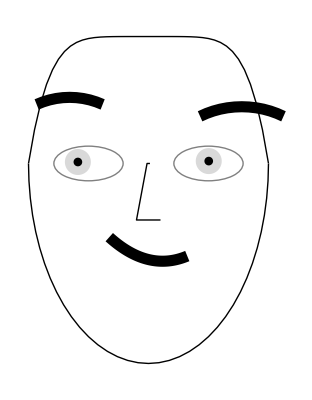

```mathematica
SeedRandom[2]
ChernoffFace[RandomReal[{0,1},17]]
```

### Scope

#### Vector argument

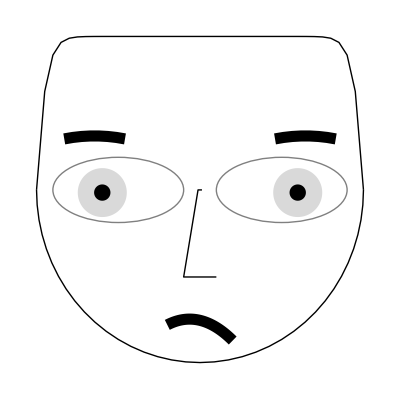

```mathematica
SeedRandom[232];
rvec=RandomReal[{-10,10},12];
ChernoffFace[rvec]
```

If the length of the vector argument is larger than the number of facial features only the first 17 elements are taken:

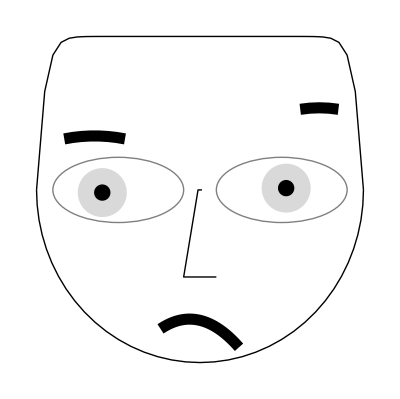
{-Graphics-,-Graphics-}

```mathematica
SeedRandom[232];
rvec=RandomReal[{-10,10},300];
ChernoffFace/@{rvec,Take[rvec,Length[ChernoffFace["FaceParts"]]]}
```

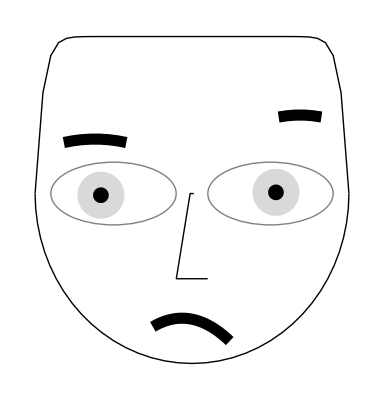

```mathematica
SeedRandom[232];
rvec=RandomReal[{0,1},30];
ChernoffFace[rvec]
```

#### List of numeric vectors

Here is a random numeric matrix (a list of vectors):

```mathematica
SeedRandom[23];
rmat=RandomVariate[SkewNormalDistribution[0,3,0.1],{25,10}];
```

Here we visualize the random matrix with Chernoff face diagrams:

```mathematica
Multicolumn[ChernoffFace[rmat,ColorFunction->"Rainbow",ImageSize->80],5]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

#### Summary

Here is a summary legend that helps the reading of the table of diagrams above:

```mathematica
ChernoffFace[rmat,"Summary",ColorFunction->"Rainbow",ImageSize->80]
```

<|QuantileChernoffFaces→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},RangeChernoffFaces→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}|>

#### Association of face parts to values

This is the “main” signature of ChernoffFace -- using an association that specifies numerical values to different face parts of the diagram:

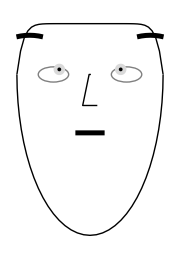

```mathematica
ChernoffFace[<|"FaceLength"->0.9,"ForeheadShape"->0.3,"EyesVerticalPosition"->0.1,"EyeSize"->0.2,"EyeSlant"->1,"LeftEyebrowSlant"->0,"LeftIris"->0.9|>,ImageSize->Small]
```

The argument association can have specifications for the face parts colors and face symmetry:

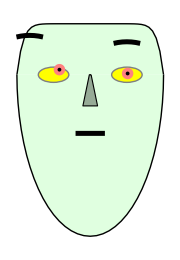

```mathematica
ChernoffFace[<|"FaceLength"->0.9,"ForeheadShape"->0.3,"EyesVerticalPosition"->0.1,"EyeSize"->0.2,"EyeSlant"->1,"LeftEyebrowSlant"->0,"LeftIris"->0.9,"FaceColor"->LightGreen,"IrisColor"->Pink,"EyeBallColor"->Yellow,"MakeSymmetric"->False|>,ImageSize->Small]
```

The order of the face parts is based on research on which diagram features influence the most how Chernoff face diagrams are perceived and comprehended.

#### Properties

Given the argument "Properties", a default association for making Chernoff face diagrams is retrieved:

```mathematica
ChernoffFace["Properties"]
```

<|FaceLength→0.5,ForeheadShape→0.5,EyesVerticalPosition→0.5,EyeSize→0.5,EyeSlant→0.5,LeftEyebrowSlant→0.5,LeftIris→0.5,NoseLength→0.5,MouthSmile→0.5,LeftEyebrowTrim→0.5,LeftEyebrowRaising→0.5,MouthTwist→0.5,MouthWidth→0.5,RightEyebrowTrim→0.5,RightEyebrowRaising→0.5,RightEyebrowSlant→0.5,RightIris→0.5,FaceColor→Automatic,IrisColor→Automatic,NoseColor→Automatic,MouthColor→Automatic,EyeBallColor→Automatic,MakeSymmetric→True|>

Use "FaceParts" or "FacePartsProperties" to get an association with only the face parts:

```mathematica
ChernoffFace["FacePartsProperties"]
```

<|FaceLength→0.5,ForeheadShape→0.5,EyesVerticalPosition→0.5,EyeSize→0.5,EyeSlant→0.5,LeftEyebrowSlant→0.5,LeftIris→0.5,NoseLength→0.5,MouthSmile→0.5,LeftEyebrowTrim→0.5,LeftEyebrowRaising→0.5,MouthTwist→0.5,MouthWidth→0.5,RightEyebrowTrim→0.5,RightEyebrowRaising→0.5,RightEyebrowSlant→0.5,RightIris→0.5|>

Here are the additional, non-numerical properties (face parts colors and symmetry):

```mathematica
KeyComplement[{ChernoffFace["Properties"],ChernoffFace["FacePartsProperties"]}]
```

<|FaceColor→Automatic,IrisColor→Automatic,NoseColor→Automatic,MouthColor→Automatic,EyeBallColor→Automatic,MakeSymmetric→True|>

#### List of associations

Here is a list of face-part-to-value associations:

```mathematica
ascs=AssociationThread[Keys[ChernoffFace["FaceParts"]⟦2;;8;;2⟧],#]&/@rmat⟦1;;5,1;;4⟧
```

{<|ForeheadShape→0.219738,EyeSize→3.3445,LeftEyebrowSlant→0.740124,NoseLength→3.57202|>,<|ForeheadShape→0.277967,EyeSize→2.99418,LeftEyebrowSlant→1.32757,NoseLength→5.06625|>,<|ForeheadShape→-1.27702,EyeSize→3.4797,LeftEyebrowSlant→4.36544,NoseLength→-0.251473|>,<|ForeheadShape→2.83725,EyeSize→0.725232,LeftEyebrowSlant→-0.284936,NoseLength→-1.72739|>,<|ForeheadShape→0.796431,EyeSize→0.0763072,LeftEyebrowSlant→2.5892,NoseLength→7.22182|>}

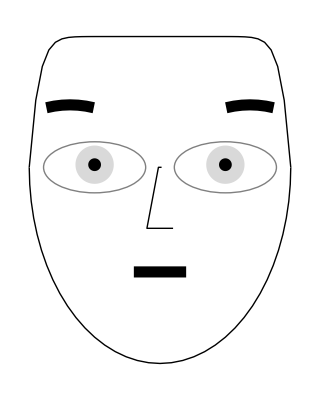
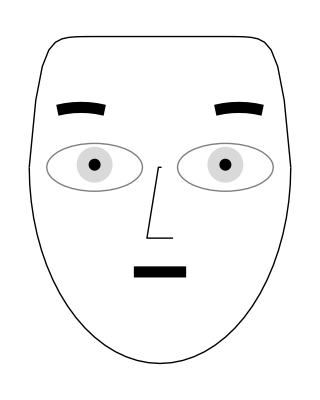
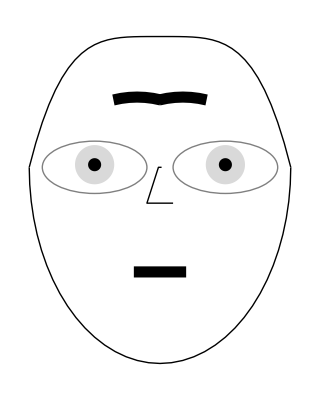
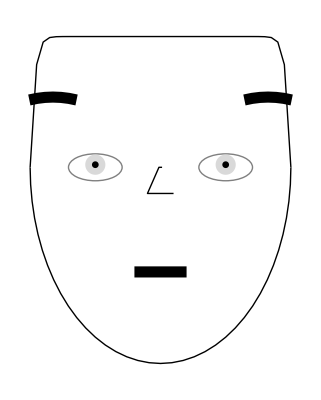
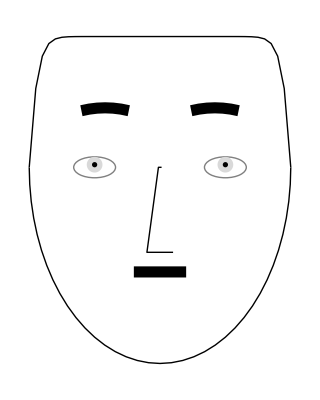

```mathematica
ChernoffFace[ascs]
```

### Options

#### ColorFunction

Using the option ColorFunction we can produce different colorings:

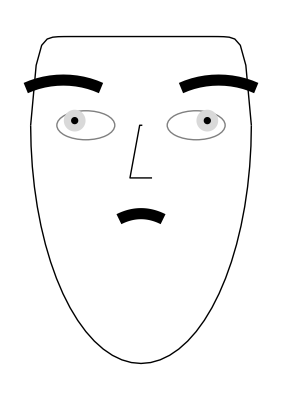
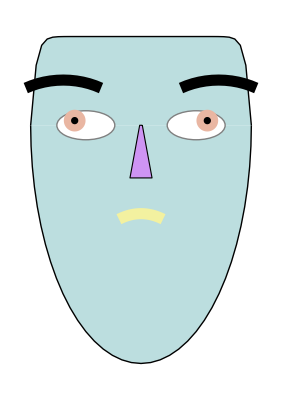
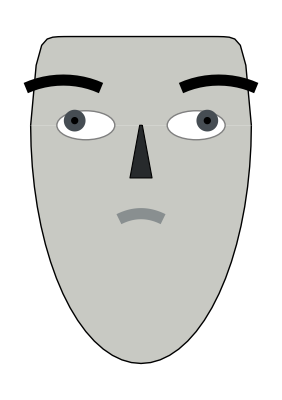
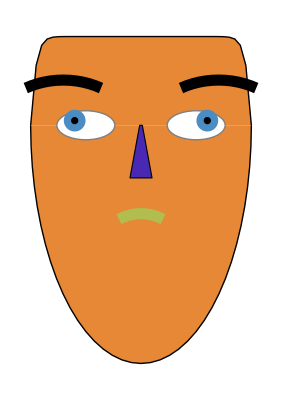
{None→-Graphics-,Automatic→-Graphics-,Pastel→-Graphics-,ColorDataFunction[…]→-Graphics-,ColorDataFunction[…]→-Graphics-}

```mathematica
SeedRandom[15];
rvec=RandomReal[{0,1},11];
#->ChernoffFace[rvec,ColorFunction->#]&/@{None,Automatic,"Pastel",ColorData["GrayTones"],ColorData["Rainbow"]}
```

The option ColorFunction assigns automatic colors to argument’s association keys:

```mathematica
Flatten@StringCases[Keys@ChernoffFace["Properties"],__~~"Color"]
```

{FaceColor,IrisColor,NoseColor,MouthColor,EyeBallColor}

#### MakeSymmetric

The faces can be made symmetric for “shorter” records.

Here is a random numeric vector:

```mathematica
SeedRandom[13];
rvec=RandomReal[{0,1},8];
```

Here are diagrams produced with different values for the option "MakeSymmetric":

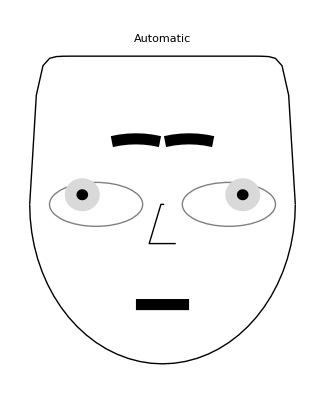
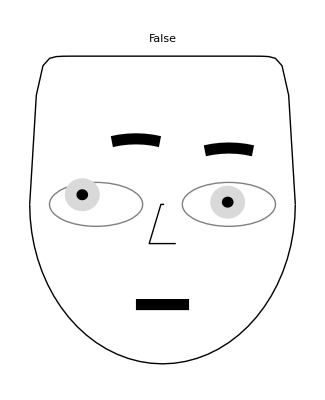
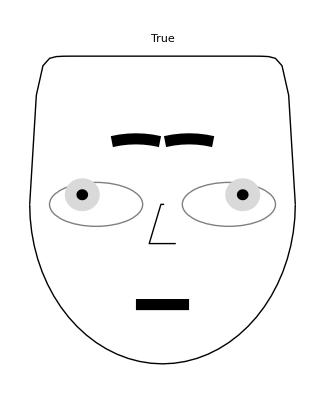

```mathematica
ChernoffFace[rvec,"MakeSymmetric"->#,PlotLabel->#]&/@{Automatic,False,True}
```

The option "MakeSymmetric" overrides argument’s association value of "MakeSymmetric":

```mathematica
avec=AssociationThread[Take[Keys[ChernoffFace["FaceParts"]],Length[rvec]]->rvec]
```

<|FaceLength→0.456535,ForeheadShape→0.86823,EyesVerticalPosition→0.704274,EyeSize→0.795001,EyeSlant→0.0405196,LeftEyebrowSlant→0.957827,LeftIris→0.00837209,NoseLength→0.251257|>

```mathematica
ChernoffFace[Append[avec,"MakeSymmetric"->True],"MakeSymmetric"->#,PlotLabel->#]&/@{Automatic,False,True}
```

{-Graphics-,-Graphics-,-Graphics-}

#### RescaleRangeFunction

If the data argument is a numeric matrix or a list of associations with numeric values then the data columns are rescaled to run between 0 and 1. The rescaling is done with Rescale using a data range finding function specified as a value to the option "RescaleRangeFunction". (By default is that is MinMax.)

Here is a random numerical matrix:

```mathematica
SeedRandom[18];
With[{m=20,n=8},
rdata=Transpose[Table[RandomVariate[SkewNormalDistribution[RandomReal[{-10,10}],RandomReal[{3,10}],RandomReal[{0,1}]],m],n]]
];
```

Here is a summary of the matrix:

```mathematica
ResourceFunction["RecordsSummary"][rdata]
```

{1 column 1
Min | -2.22775
1st Qu | 3.64573
Median | 9.70393
Mean | 10.8059
3rd Qu | 15.8937
Max | 26.4213,2 column 2
Min | -3.70973
1st Qu | 4.1529
Mean | 7.73045
Median | 8.3109
3rd Qu | 11.9658
Max | 16.8468,3 column 3
Min | -16.2457
1st Qu | -10.4237
Mean | -6.28032
Median | -5.85438
3rd Qu | -4.16792
Max | 6.81017,4 column 4
Min | 2.68056
1st Qu | 3.97422
Mean | 5.89804
Median | 5.90653
3rd Qu | 7.16374
Max | 11.7735,5 column 5
Min | -10.7326
1st Qu | -2.16796
Mean | 3.01345
Median | 3.34552
3rd Qu | 8.59922
Max | 19.115,6 column 6
Min | -4.9151
1st Qu | -2.49652
Median | -0.280755
Mean | -0.0287502
3rd Qu | 1.82274
Max | 5.58613,7 column 7
Min | -13.3835
1st Qu | -0.74332
Mean | 6.22388
Median | 9.61872
3rd Qu | 13.5271
Max | 16.2779,8 column 8
Min | 3.99707
1st Qu | 9.92579
Median | 13.2697
Mean | 14.2962
3rd Qu | 18.9899
Max | 26.6449}

Here is a list of Chernoff face diagrams produced with the default value for the option "RescaleRangeFunction":

```mathematica
cf1=ChernoffFace[rdata,ImageSize->80,ColorFunction->"Rainbow", "RescaleRangeFunction"->MinMax]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Here is a list of Chernoff face diagrams produced by making the ranges of the matrix columns slightly wider than they are:

```mathematica
cf2=ChernoffFace[rdata,ImageSize->80,ColorFunction->"Rainbow","RescaleRangeFunction"->({-1,1}+MinMax[#]&)]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Applications

#### Visualizing the "EmployeeAttitude" dataset

In order to study a dataset with Chernoff face diagrams we have to provide (1) a list of Chernoff face diagrams, (2) a legend that shows how the face features are mapped to dataset’s columns, and (3) a legend that shows Chernoff face diagrams for easy to understand instances of the dataset.

Get the "EmployeeAttitude" data:

```mathematica
data=ExampleData[{"Statistics","EmployeeAttitude"}];
Dimensions[data]
```

{30,7}

Get the corresponding column names:

```mathematica
dataColumnNames=ExampleData[{"Statistics","EmployeeAttitude"},"ColumnHeadings"]
```

{Rating,Complaints,Privileges,Learning,Raises,Critical,Advancement}

Here is a summary of the dataset:

```mathematica
ResourceFunction["RecordsSummary"][data,dataColumnNames]
```

{1 Rating
Min | 40
1st Qu | 58
Mean | 64.6333
Median | 65.5
3rd Qu | 72
Max | 85,2 Complaints
Min | 37
1st Qu | 58
Median | 65
Mean | 66.6
3rd Qu | 77
Max | 90,3 Privileges
Min | 30
1st Qu | 45
Median | 51.5
Mean | 53.1333
3rd Qu | 64
Max | 83,4 Learning
Min | 34
1st Qu | 47
Mean | 56.3667
Median | 56.5
3rd Qu | 67
Max | 75,5 Raises
Min | 43
1st Qu | 58
Median | 63.5
Mean | 64.6333
3rd Qu | 71
Max | 88,6 Critical
Min | 49
1st Qu | 68
Mean | 74.7667
Median | 77.5
3rd Qu | 80
Max | 92,7 Advancement
Min | 25
1st Qu | 35
Median | 41
Mean | 42.9333
3rd Qu | 48
Max | 72}

Visualize with Chernoff faces:

```mathematica
Legended[
Grid[Partition[ChernoffFace[data,ColorFunction->"Rainbow",ImageSize->100],6],Dividers->All],
Placed[Framed[Grid[Thread[{Take[Keys@ChernoffFace["FaceParts"],Length[dataColumnNames]],dataColumnNames}],Alignment->{{Right,Left}}]],"Right"]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Make a table of records summary diagrams:

```mathematica
Grid[Flatten@*List@@@Normal[ChernoffFace[data,"RecordsSummary",ImageSize->80,ColorFunction->"Rainbow"]],Dividers->All]
```

QuantileChernoffFaces | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
RangeChernoffFaces | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

We can see that: (1) higher learning is associated with higher ratings; (2) the higher the privileges the higher the ratings. (Other observations can be made…)

### Properties and Relations

It is a good idea to compare the diagrams made with ChernoffFace with diagrams made with SectorChart:

```mathematica
SeedRandom[1612]
rmat=Transpose@Table[RandomVariate[SkewNormalDistribution[RandomReal[{1,10}],RandomReal[{1,4}],RandomReal[{0.2,0.8}]],12],5];
Multicolumn[Map[Row[{Image[ChernoffFace[#,ColorFunction->"Pastel"],ImageSize->80],Image[SectorChart[Transpose[{Range[Length[#]],#}],ChartLabels->Placed[Range[Length[#]],"RadialOutside"]],ImageSize->120]}]&,Rescale/@rmat],4,Dividers->All]
```

-Graphics-

### Possible Issues

#### Record-wise vs. en bloc

ChernoffFace invoked over an association or a list of numbers rescales the values of the argument data to run from 0 to 1 over the range Min[data]to Max[data]. ChernoffFace called on a list of associations or a matrix rescales the columns of the corresponding full array. Hence, in general, the diagrams produced by invoking ChernoffFace record-wise over a list of records are different from the diagrams produced by invoking ChernoffFace over the whole data set of records.

Here is a random numeric matrix (list of records):

```mathematica
SeedRandom[18];
rdata=RandomReal[{-10,10},{10,12}];
```

Here are Chernoff face diagrams made separately for each record:

```mathematica
ChernoffFace[#,ImageSize->80,ColorFunction->"Rainbow"]&/@rdata
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Here are Chernoff face diagrams made for the whole array:

```mathematica
ChernoffFace[rdata,ImageSize->80,ColorFunction->"Rainbow"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

We see that although the diagrams from the two lists are similar they also have notable differences. With different data distributions the differences will be greater or smaller.

#### Different perceptions with different color schemes

The same data visualized with different color schemes might make certain items or features more obscure or more prominent.

Using the "BrightBands" color scheme makes all diagrams to look unique:

```mathematica
ChernoffFace[rdata,ImageSize->80,ColorFunction->"BrightBands"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Using the "WatermelonColors" color scheme over the same data makes the first and the last diagram to stand out:

```mathematica
ChernoffFace[rdata,ImageSize->80,ColorFunction->"WatermelonColors"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Neat Examples

A table of random Chernoff faces:

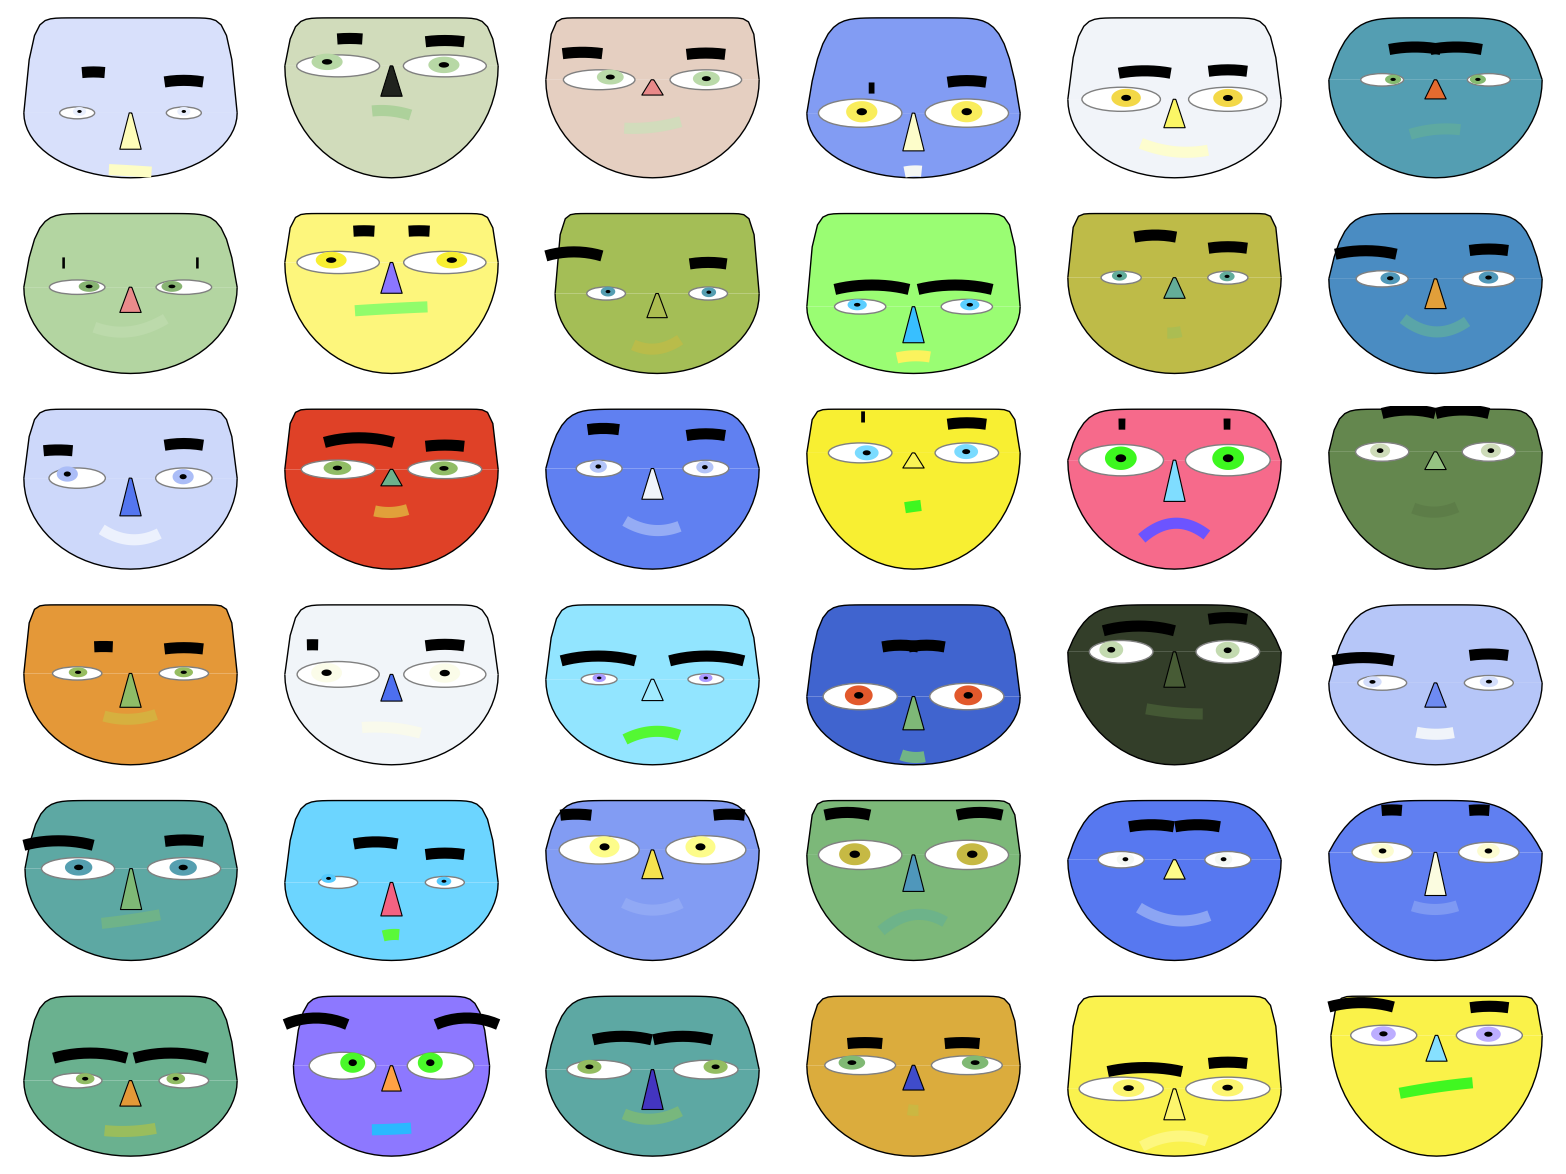

```mathematica
SeedRandom[7783];
Grid[Table[ChernoffFace[ColorFunction->RandomChoice[{"Rainbow","BrightBands","WatermelonColors","TemperatureMap"}],"MakeSymmetric"->RandomChoice[{True,False}],ImageSize->Tiny],{6},{6}]]
```

## Source & Additional Information

### Contributed ByContributed ByEnter the name of the person, people or organization that should be publicly credited with contributing this function.

Anton Antonov

### KeywordsKeywordsList relevant terms (e.g. functional areas, algorithm names, related concepts) that should be used to include the function in search results.

Chernoff face

Multi-dimensional data

Data visualization

### Categories

Data Manipulation & Analysis

Visualization & Graphics

### Related SymbolsRelated SymbolsList up to twenty documented, system-level Wolfram Language symbols related to the function.

Rescale

Graphics

Standardize

Quantile

### Related Resource ObjectsRelated Resource ObjectsList the names of published resource objects from any Wolfram repository that are related to this function.

RecordsSummary

### Source/Reference CitationSource/Reference CitationGive a bibliographic-style citation for the original source of the function and/or its components (e.g. a published paper, algorithm, or code repository).

Anton Antonov, Making Chernoff faces for data visualization, 2016, MathematicaForPrediction at WordPress.
Christopher J. Morris; David S. Ebert; Penny L. Rheingans, “Experimental analysis of the effectiveness of features in Chernoff faces”, Proc. SPIE 3905, 28th AIPR Workshop: 3D Visualization for Data Exploration and Decision Making, (5 May 2000); doi: 10.1117/12.384865.

### LinksLinksList additional URLs or hyperlinks for external information related to the function.

https://mathematicaforprediction.wordpress.com/2016/06/03/making-chernoff-faces-for-data-visualization/

https://en.wikipedia.org/wiki/Chernoff_face

### TestsTestsSpecify an optional list of tests for verifying that the function is working properly in any environment. Tests can be specified as Input/Output cell pairs or as symbolic VerificationTest expressions for including additional options.

```mathematica
SeedRandom[1425];
{dists,data}=Transpose[Table[(rdist=RandomChoice[{NormalDistribution[RandomReal[10],RandomReal[10]],PoissonDistribution[RandomReal[4]],BetaDistribution[RandomReal[2],1.5]}];
{rdist,RandomVariate[rdist,12]}),{12}]];
MatrixQ[data,NumericQ]
```

True

```mathematica
VerificationTest[(*3*)
Head/@Table[ChernoffFace[],36],
Table[Graphics,36],
TestID->"NoArguments-1"
]
```

TestResultObject[…]

```mathematica
VerificationTest[(*4*)
Head/@Table[ChernoffFace[ColorFunction->ColorData["BrightBands"],ImageSize->Tiny],36],
Table[Graphics,36],
TestID->"ColorFunction-1"
]
```

TestResultObject[…]

```mathematica
VerificationTest[(*7*)
Head/@Map[ChernoffFace,data],
Table[Graphics,Length[data]],
TestID->"NumericMatrix-1"
]
```

TestResultObject[…]

```mathematica
VerificationTest[(*7*)
Head/@ChernoffFace[data],
Table[Graphics,Length[data]],
TestID->"NumericMatrix-1"
]
```

TestResultObject[…]

```mathematica
VerificationTest[(*20*)
Head/@ChernoffFace[data,ColorFunction->ColorData["BrightBands"]],
Table[Graphics,Length[data]],
TestID->"NumericMatrix-ColorFunction-1"
]
```

TestResultObject[…]

```mathematica
VerificationTest[(*21*)
gr1=Map[ChernoffFace[#,ColorFunction->ColorData["BrightBands"]]&,VariablesRescale[data]];
gr2=ChernoffFace[data,ColorFunction->ColorData["BrightBands"]];
gr1==gr2,
True,
TestID->"NumericMatrix-ColorFunction-2"
]
```

TestResultObject[…]

## Author Notes

The idea to use human faces in order to understand, evaluate, or easily discern (the records of) multidimensional data is very creative and inspirational. I personally find the use of Chernoff face diagrams useful in a small number of cases, but that is probably true for many “creative” data visualization methods.

A fundamental restriction of using Chernoff face diagrams is the necessity to properly transform the data variables into the ranges of the Chernoff face diagram parameters. Therefore, proper data transformation (standardizing and rescaling) is an inherent part of the application of Chernoff face diagrams.

The order of the face parts is based on some research which Chernoff face diagram features influence the most diagram’s comprehension. See the article:

Christopher J. Morris; David S. Ebert; Penny L. Rheingans, “Experimental analysis of the effectiveness of features in Chernoff faces”, Proc. SPIE 3905, 28th AIPR Workshop: 3D Visualization for Data Exploration and Decision Making, (5 May 2000); doi: 10.1117/12.384865.

## Submission NotesSubmission NotesEnter any additional information that you would like to communicate to the reviewer here. This section will not be included in the published resource.

Additional information for the reviewer.